0

1

ⅇ^t

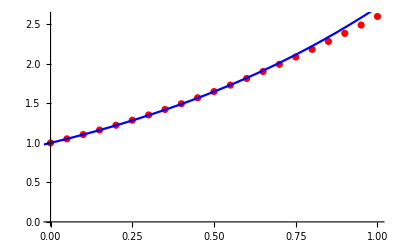

```mathematica
a =0
b = 1 
(*Ядро*)K[t_,s_] := t-s;
(*Точное решение*) sol1=DSolveValue[x[t]-Integrate[K[t,s]*x[s], {s, a, t}] ==1+ t, x[t], t]

(*Лист точек х*)x1 ={0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1};
(*Лист точек f(x)*)fx1 ={1,1.0515,1.10601,1.16352,1.22404,1.28757,1.3541,1.42363,1.49617,1.57172,1.65027,1.73183,1.81639,1.90396,1.99454,2.08811,2.1847,2.28429,2.38689,2.49249,2.60109};
p1=ListPlot[Transpose[{x1,fx1}],PlotStyle->Red];
p2=Plot [sol1, {t, -1, 1}, PlotStyle->Blue];
(*Итоговый график*)Show[p1,p2]
```